```mathematica
f[x_]:=(1-2x^2)(UnitStep[x]-UnitStep[x-1/2])+2(x-1)^2(UnitStep[x-1/2]-UnitStep[x-1])
```

```mathematica
f[x]
```

2 (-1+x)^2 (-UnitStep[-1+x]+UnitStep[-1/2+x])+(1-2 x^2) (-UnitStep[-1/2+x]+UnitStep[x])

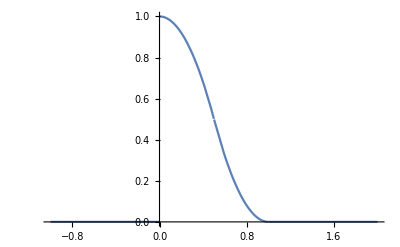

```mathematica
Plot[f[x],{x,-1,2}]
```

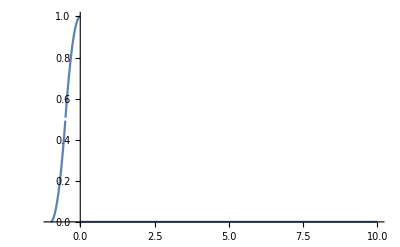

```mathematica
Plot[f[-x],{x,-1,10}]
```

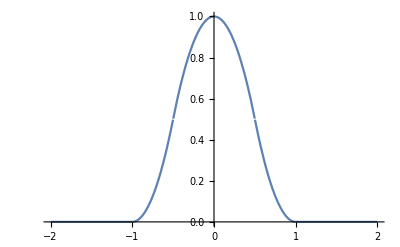

```mathematica
Plot[f[-x]+f[x],{x,-2,2}]
```

```mathematica
g[x_]:=f[-x]+f[x]
```

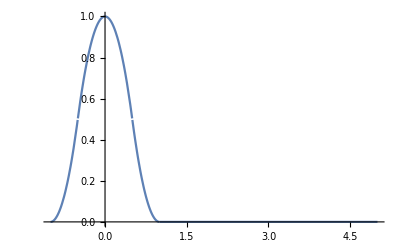

```mathematica
Plot[g[x],{x,-1,5}]
```

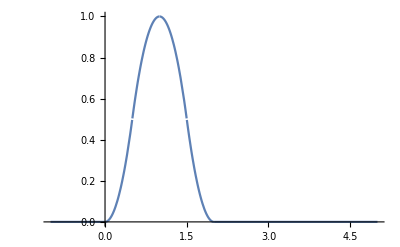

```mathematica
Plot[g[x-1],{x,-1,5}]
```

```mathematica
k[x_]:=f[-x]
```

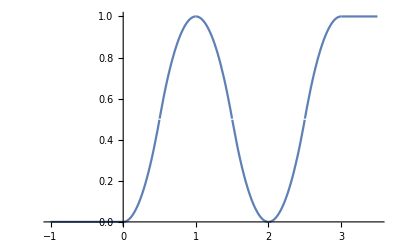

```mathematica
Plot[g[x-1]+k[x-3]+UnitStep[x-3],{x,-1,3.5}]
```

```mathematica
G[x_]:=(1-2x^2)(UnitStep[-x]-UnitStep[-x-1/2])+2(-x-1)^2(UnitStep[-x-1/2]-UnitStep[-x-1])+UnitStep[x]
```

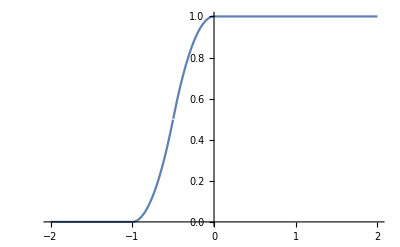

```mathematica
Plot[G[x],{x,-2,2}]
```

```mathematica
G[0]
```

2

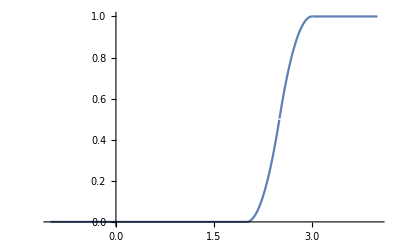

```mathematica
Plot[G[x-3],{x,-1,4}]
```

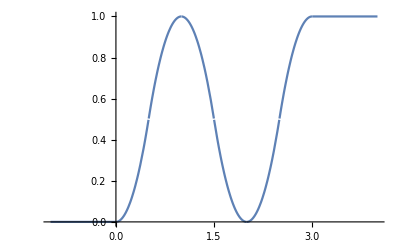

```mathematica
Plot[g[x-1]+G[x-3],{x,-1,4}]
```

```mathematica
"the following function, g1[x_], is the final version of the activation function g[x_], i.e., g[x_]+g1[x]"
```

the following function, g1[x_], is the final version of the activation function g[x_], i.e., g[x_]+g1[x]

```mathematica
g1[x_]:=(4x-2x^2-1)(UnitStep[x-1]-UnitStep[x-3/2])+2(x-2)^2(UnitStep[x-3/2]-UnitStep[x-2])+

    (4x-2x^2-1)(UnitStep[1-x]-UnitStep[1/2-x])+2x^2(UnitStep[1/2-x]-UnitStep[-x])+
     (1-2(x-3)^2)(UnitStep[3-x]-UnitStep[3-x-1/2])+2(2-x)^2(UnitStep[3-x-1/2]-UnitStep[2-x])+UnitStep[x-3]
```

```mathematica
Plot[g1[x],{x,-1,4}]
```

-Graphics-

```mathematica
---------------------------------------------------------------------------------------------------------------
```

```mathematica
(* Using "If' statements, which is much simplere to   write down. 08/19/20. *)
```

```mathematica
g[x_]:= If[0<=x<1/2,2x^2,0]+If[1/2≤x<3/2,1-2(x-1)^2,0]+If[3/2≤x<5/2,2(x-2)^2,0]+ If[5/2≤x<3,1-2(x-3)^2,0]+If[3≤x,1,0]
```

```mathematica
h[x_]:= If[0<=x<1/2,4x,0]+If[1/2≤x<3/2,4-4x,0]+If[3/2≤x<5/2,4x-8,0]+If[5/2≤x<3,12-4x,0]
```

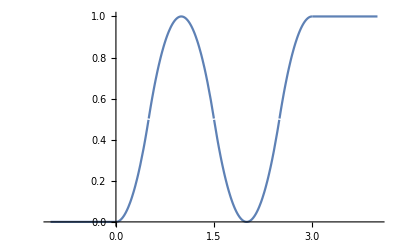

```mathematica
Plot[g[x],{x,-1,4}]
```

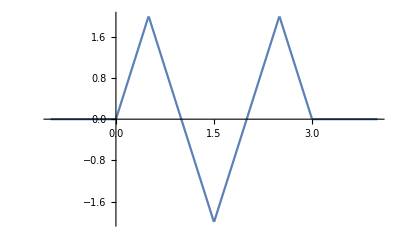

```mathematica
Plot[h[x],{x,-1,4}]
```

```mathematica
(n=1;
 b=0.917305115543521;
{w1,w2}={0.5921908684844923,0.20764932665001293};
eta=0.01;
max=250;
g[x_]:=If[0<=x<1/2,2x^2,0]+If[1/2≤x<3/2,1-2(x-1)^2,0]+If[3/2≤x<5/2,2(x-2)^2,0]+
              If[5/2≤x<3,1-2(x-3)^2,0]+If[3≤x,1,0];
h[x_]:=If[0<=x<1/2,4x,0]+If[1/2≤x<3/2,4-4x,0]+If[3/2≤x<5/2,4x-8,0]+If[5/2≤x<3,12-4x,0];
Label[1];
x1=RandomInteger[];
x2=RandomInteger[];
n=n+1;
b=b-eta(-(g[x1+x2]-g[b+w1 x1+w2 x2]))h[b+w1 x1+w2 x2];
w1=w1-eta(-x1(g[x1+x2]-g[b+w1 x1+w2 x2]))h[b+w1 x1+w2 x2];
w2=w2-eta(-x2(g[x1+x2]-g[b+w1 x1+w2 x2]))h[b+w1 x1+w2 x2];
If[n<max,Goto [1]];
Print[{(g[x1+x2]-g[w1 x1+w2 x2])^2/4,{x1,x2},{w1,w2},g[w1 x1+w2 x2],max}];
)
```

{0.215173,{1,1},{0.710885,0.4792},0.927735,250}